## Seasonal Ricker model - EWS in rnb - Singles

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Google\ Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_seasonal"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=-2;
bh=-0.0568;
```

## Import Data

```mathematica
(* Name of simluation run *)
simName="trans_rnb_tmax400";
```

```mathematica
(* Import EWS DataFrame *)
dfEws=Import["data_export/"<>simName<>"/ews_singles.csv"];
```

```mathematica
(* Import power spectrum DataFrame *)
dfPspec=Import["data_export/"<>simName<>"/pspec.csv"];
```

```mathematica
(* Import ews means DataFrame *)
dfEwsMeans=Import["data_export/"<>simName<>"/ews_means.csv"];
```

```mathematica
(* Import ews sd DataFrame *)
dfEwsSd=Import["data_export/"<>simName<>"/ews_deviations.csv"];
```

```mathematica
(* Import Kendall tau values *)
dfKtau=Import["data_export/"<>simName<>"/ktau.csv"];
```

```mathematica
numSims=Length[Union[dfEws[[2;;,1]]]]
```

5

```mathematica
(* Realisation number to display *)
displayNum=2;
```

## Figure params

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* Extract info *)
realNum=1;
seriesB = Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Breeding",_,_}][[;;,{3,4}]];
seriesNB = Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Non-breeding",_,_}][[;;,{3,4}]];
seriesTotal= Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Total",_,_}][[;;,{3,4}]];
```

```mathematica
(* Useful info *)
tVals=seriesB[[;;,1]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
realMax=Max[dfEws[[;;,1]]][[1]];
stateVals=Union[dfEws[[2;;,2]]];
```

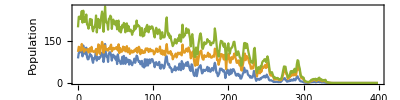

```mathematica
(* plot of breeding series *)
plotPop = ListPlot[{seriesB,seriesNB,seriesTotal},
Joined->True,
LabelStyle->12,
PlotLegends->Placed[trajLegend,Scaled[{0.85,0.7}]],
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Breeding growth rate, r_b"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
AxesLabel->{"t","Population"},
PlotRange->{{0,tmax},All}]
```

```mathematica
(* line legend *)
trajLegend=LineLegend[TMBcolours[[1;;3]],{"Breeding","Non-breeding","Total"},Spacings->{0,0.2},LabelStyle->10]
```

### Output

```mathematica
rTicks=Range[bl,bh,0.2];
rTicksT=(rTicks-bh)*tmax/(bl-bh);
```

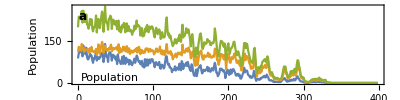

```mathematica
plotTraj=Show[{plotPop},
PlotRange->{{0,tmax*1.05},{-5,All}},
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Non-breeding growth rate, r_nb"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{rTicksT,rTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Population",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}]}
]
```

## EWS Plots (Mean +/- SD)

### Variance

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Variance"][[1,1]];
```

```mathematica
ewsVals=Table[Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}],{state,stateVals}][[;;,;;,{3,4}]];
```

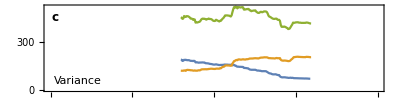

```mathematica
(* Plot EWS *)
plotVar=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Variance",ls],textPos,{-1,0}]}]
```

### Coefficient of variation

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
ewsVals=Table[Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}],{state,stateVals}][[;;,;;,{3,4}]];
```

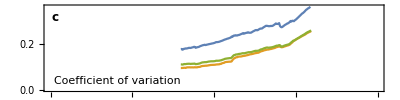

```mathematica
(* Plot EWS *)
plotCv=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}]
```

### Smax/Var

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Var"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

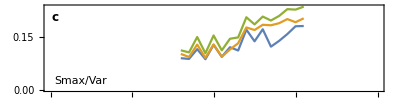

```mathematica
(* Plot EWS *)
plotSmaxVar=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Smax/Var",ls],textPos,{-1,0}]}]
```

### Skewness

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Skewness"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

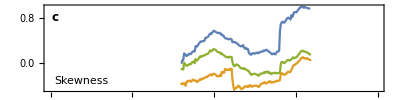

```mathematica
(* Plot EWS *)
plotSkew=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Skewness",ls],textPos,{-1,0}]}]
```

### Lag-1 AC

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

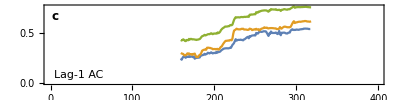

```mathematica
(* Plot EWS *)
plotAc1=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameLabel->{{"",""},{"Time (arbitrary units)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Lag-1 AC",ls],textPos,{-1,0}]}]
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

### Variance

```mathematica
indexKtau=Position[dfKtau[[1]],"Variance"][[1,1]]
```

12

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.886502 | -0.964652 | -0.681091 | -0.96051 | -0.947229 | -0.869597 | -0.972279 | -0.973035 | -0.880066 | -0.952315 | -0.953085 | -0.973547 | -0.977458 | -0.914921 | -0.882754 | -0.793201 | -0.977668 | -0.927195 | -0.976471 | -0.949153 | -0.970007 | -0.885044 | -0.977536 | -0.951918 | -0.97756 | -0.925943 | -0.944726 | -0.916187 | -0.927253 | -0.884207 | -0.938354 | -0.821632 | -0.95648 | -0.889806 | -0.857483 | -0.963925 | -0.837916 | -0.952964 | -0.864425 | -0.850796 | -0.928487 | -0.873256 | -0.913514 | -0.980606 | -0.921411 | -0.938211 | -0.757782 | -0.96115 | -0.794099 | -0.77218 | -0.943294 | -0.857803 | -0.94012 | -0.902452 | -0.917785 | -0.923117 | -0.752535 | -0.734078 | -0.945863 | -0.604022 | -0.925584 | -0.893247 | -0.868038 | -0.948823 | -0.850681 | -0.940286 | -0.946282 | -0.965311 | -0.954229 | -0.949881 | -0.752656 | -0.979006 | -0.921684 | -0.969813 | -0.972677 | -0.749425 | -0.889862 | -0.917558 | -0.856801 | -0.951875 | -0.806808 | -0.972062 | -0.912138 | -0.974136 | -0.973883 | -0.735064 | -0.61003 | -0.962773 | -0.908945 | -0.874892 | -0.910022 | -0.945288 | -0.767094 | -0.930452 | -0.932012 | -0.936652 | -0.915582 | -0.905313 | -0.959989 | -0.73032
Non-breeding | 0.766494 | 0.760535 | 0.880258 | 0.740565 | 0.905928 | 0.877688 | 0.563845 | 0.559195 | 0.785399 | 0.802727 | 0.64497 | 0.438127 | 0.514827 | 0.883851 | 0.819692 | 0.929766 | 0.725714 | 0.572461 | 0.761866 | 0.816289 | 0.691904 | 0.704715 | 0.28025 | 0.611421 | 0.707084 | 0.897671 | 0.584285 | 0.655914 | 0.87151 | 0.853423 | 0.922092 | 0.740812 | 0.769189 | 0.935746 | 0.776577 | 0.628713 | 0.737543 | 0.834072 | 0.45757 | 0.868155 | 0.648135 | 0.919274 | 0.231386 | 0.611215 | 0.759528 | 0.760935 | 0.679036 | 0.906132 | 0.752638 | 0.674194 | 0.7807 | 0.445949 | 0.839321 | 0.544721 | 0.729225 | 0.870185 | 0.579535 | 0.787968 | 0.807317 | 0.894955 | 0.887857 | 0.758218 | 0.666841 | 0.43458 | 0.716583 | 0.38097 | 0.845381 | 0.798145 | 0.764933 | 0.521821 | 0.690867 | 0.779491 | 0.860841 | 0.627776 | 0.736104 | 0.961266 | 0.855679 | 0.76651 | 0.845381 | 0.876553 | 0.798576 | 0.791603 | 0.547503 | 0.378971 | 0.734781 | 0.803837 | 0.685209 | 0.854149 | 0.569866 | 0.777576 | 0.763554 | 0.801016 | 0.920115 | 0.8858 | 0.556149 | 0.751084 | 0.861537 | 0.905859 | 0.653324 | 0.641711
Total | 0.496623 | -0.225 | 0.505032 | 0.225422 | 0.502858 | -0.237936 | 0.0582496 | -0.179077 | 0.674179 | 0.540649 | -0.33505 | -0.0490524 | 0.060355 | 0.566278 | 0.531199 | 0.815964 | -0.575584 | 0.0820229 | -0.160887 | 0.430585 | -0.424568 | 0.0115798 | -0.750916 | -0.154811 | -0.486221 | 0.401087 | 0.213136 | 0.558162 | 0.618892 | 0.437072 | 0.776398 | 0.390374 | 0.412421 | 0.19873 | 0.155978 | 0.0907294 | 0.491396 | 0.444489 | 0.0864965 | 0.576381 | 0.337135 | 0.67423 | -0.601976 | 0.140535 | 0.446182 | 0.243373 | 0.20799 | 0.634119 | 0.259338 | 0.511579 | -0.0388519 | -0.0359943 | 0.571571 | -0.368455 | 0.137255 | 0.764381 | 0.237255 | 0.697483 | 0.552526 | 0.670637 | 0.627623 | 0.23793 | 0.242197 | -0.0121206 | 0.567232 | -0.340945 | 0.653806 | 0.447105 | 0.245989 | -0.0830979 | 0.396025 | -0.47022 | 0.688613 | 0.16528 | -0.597403 | 0.78479 | 0.58111 | 0.534195 | 0.320473 | 0.414923 | 0.646083 | 0.504345 | -0.0146774 | -0.322885 | -0.381788 | 0.702412 | 0.485493 | 0.438837 | -0.0745098 | 0.633246 | 0.283497 | 0.196807 | 0.781992 | 0.555461 | 0.330508 | 0.467492 | 0.500782 | 0.778342 | 0.107135 | 0.529298

```mathematica
(* Box plot *)
boxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Skewness

```mathematica
indexKtau=Position[dfKtau[[1]],"Skewness"][[1,1]]
```

9

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.103711 | 0.297508 | 0.768686 | 0.633821 | -0.473118 | -0.40464 | 0.244857 | 0.488829 | 0.0124069 | -0.121314 | -0.298676 | 0.616341 | -0.0259228 | 0.483312 | -0.21639 | 0.682296 | 0.610903 | -0.0777164 | -0.369797 | 0.505521 | -0.218576 | 0.519732 | 0.762735 | 0.609441 | 0.928601 | 0.906761 | 0.581295 | 0.543737 | -0.0181317 | 0.517393 | 0.284783 | 0.678569 | 0.687203 | 0.499871 | 0.33245 | 0.753937 | 0.798682 | -0.142414 | 0.663599 | 0.664647 | 0.925042 | 0.634443 | -0.271563 | 0.754113 | 0.724813 | 0.799704 | 0.823373 | 0.503383 | 0.821658 | 0.818766 | 0.29816 | 0.840389 | -0.0299401 | 0.736015 | 0.934297 | -0.199481 | 0.692065 | 0.569336 | 0.49145 | -0.801257 | 0.353085 | -0.699351 | 0.152409 | -0.200105 | 0.216157 | 0.00273122 | -0.435134 | -0.347875 | 0.788166 | 0.718425 | 0.754478 | 0.193247 | -0.206392 | -0.0506266 | 0.555862 | 0.636782 | 0.305837 | 0.261701 | 0.79201 | 0.444818 | 0.857907 | 0.632225 | 0.510436 | 0.747556 | 0.617359 | 0.655728 | 0.86663 | 0.506096 | 0.0366864 | 0.569408 | 0.857938 | 0.341173 | -0.462704 | 0.524277 | 0.876394 | -0.531082 | 0.0523643 | 0.136238 | 0.728515 | 0.70456
Non-breeding | 0.640649 | 0.342767 | 0.17729 | 0.57469 | 0.41091 | -0.834687 | 0.561167 | 0.262617 | 0.630573 | -0.140519 | 0.425409 | 0.67159 | 0.735244 | 0.659542 | 0.259913 | 0.396828 | 0.228052 | 0.742821 | 0.472052 | 0.235828 | 0.040363 | 0.282382 | 0.600913 | 0.174922 | 0.631805 | 0.71118 | 0.487945 | -0.385084 | 0.45986 | 0.672499 | 0.347289 | 0.121743 | 0.271676 | -0.754159 | 0.146392 | 0.184888 | -0.206045 | -0.207127 | 0.825916 | 0.653114 | 0.190544 | 0.38938 | 0.385295 | 0.708846 | 0.311111 | -0.133844 | -0.192129 | 0.48695 | 0.626889 | 0.348676 | 0.59731 | 0.782015 | 0.682207 | 0.537522 | 0.714116 | 0.801361 | -0.110791 | 0.848864 | 0.72885 | -0.292969 | 0.50688 | 0.103364 | 0.672305 | 0.536724 | 0.4139 | 0.720933 | 0.162454 | -0.33892 | 0.694049 | 0.372475 | 0.662523 | 0.453949 | 0.619183 | 0.837862 | 0.832078 | 0.782333 | 0.793763 | -0.168508 | 0.17354 | -0.064514 | 0.674403 | 0.591238 | 0.812038 | 0.601153 | 0.794375 | -0.172837 | 0.758835 | -0.28714 | 0.128586 | 0.0196037 | 0.790303 | 0.489801 | 0.301149 | 0.41075 | -0.0627943 | -0.204128 | 0.81295 | 0.729004 | 0.309572 | -0.540448
Total | 0.218442 | -0.0366352 | 0.0270968 | 0.414966 | -0.161522 | -0.802676 | 0.407365 | 0.119406 | -0.210518 | -0.244805 | -0.505743 | 0.777964 | -0.125096 | 0.57513 | 0.0614993 | 0.0967236 | -0.112208 | -0.473135 | -0.47178 | -0.309846 | -0.2499 | 0.552854 | 0.630217 | -0.0597145 | 0.817852 | 0.863509 | 0.160144 | -0.514577 | 0.421684 | 0.365154 | 0.339314 | -0.00295824 | 0.0969216 | -0.298032 | -0.345242 | -0.0764313 | -0.157115 | -0.463194 | 0.79483 | 0.258167 | 0.362913 | 0.285726 | -0.266609 | 0.706064 | 0.227809 | -0.271267 | 0.613647 | 0.467296 | 0.0761334 | 0.717481 | 0.345103 | 0.790568 | 0.339607 | 0.655432 | 0.763348 | 0.656009 | -0.409115 | 0.763536 | 0.602818 | -0.379653 | 0.0550396 | -0.510144 | 0.332636 | 0.330778 | 0.0984794 | 0.364027 | -0.428381 | -0.611701 | 0.788827 | 0.22428 | 0.24338 | -0.585453 | 0.292533 | 0.796859 | 0.397922 | 0.308077 | 0.730609 | -0.342303 | 0.189948 | -0.502093 | 0.596984 | 0.681198 | 0.805097 | 0.278809 | 0.741242 | -0.460075 | 0.786976 | -0.354862 | -0.594634 | -0.234122 | 0.731709 | 0.322099 | -0.400383 | 0.199743 | 0.376766 | -0.501754 | 0.320405 | 0.552694 | 0.532892 | -0.747753

```mathematica
(* Box plot *)
boxSkew=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Coefficient of variation

```mathematica
indexKtau=Position[dfKtau[[1]],"Coefficient of variation"][[1,1]]
```

4

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.976617 | 0.96927 | 0.988985 | 0.966745 | 0.974359 | 0.882784 | 0.952767 | 0.951464 | 0.981803 | 0.927619 | 0.938433 | 0.963698 | 0.944914 | 0.976549 | 0.990305 | 0.990287 | 0.94023 | 0.97299 | 0.963399 | 0.981767 | 0.936467 | 0.944533 | 0.982272 | 0.961082 | 0.96124 | 0.979403 | 0.986361 | 0.989422 | 0.982034 | 0.980565 | 0.959783 | 0.974815 | 0.978784 | 0.984774 | 0.98234 | 0.985076 | 0.973491 | 0.978932 | 0.985891 | 0.959135 | 0.986695 | 0.980005 | 0.940071 | 0.986925 | 0.991965 | 0.977531 | 0.983034 | 0.979938 | 0.981675 | 0.979847 | 0.973529 | 0.969135 | 0.979078 | 0.984789 | 0.979704 | 0.977273 | 0.984336 | 0.98833 | 0.982363 | 0.951739 | 0.96741 | 0.980909 | 0.975793 | 0.979487 | 0.988229 | 0.93594 | 0.985186 | 0.977581 | 0.974355 | 0.977901 | 0.991136 | 0.855985 | 0.989548 | 0.946644 | 0.956388 | 0.98295 | 0.972466 | 0.979924 | 0.978154 | 0.961285 | 0.991851 | 0.980636 | 0.988845 | 0.924109 | 0.960149 | 0.991776 | 0.994268 | 0.980521 | 0.953777 | 0.984024 | 0.974522 | 0.976482 | 0.981935 | 0.959743 | 0.981708 | 0.981204 | 0.973553 | 0.979408 | 0.974782 | 0.9885
Non-breeding | 0.988831 | 0.990094 | 0.996129 | 0.988817 | 0.992651 | 0.961777 | 0.987088 | 0.972577 | 0.997714 | 0.991429 | 0.983571 | 0.976589 | 0.980468 | 0.993847 | 0.989226 | 0.981352 | 0.979091 | 0.996114 | 0.977424 | 0.996826 | 0.994586 | 0.958478 | 0.991833 | 0.993917 | 0.977282 | 0.994565 | 0.995939 | 0.99747 | 0.99062 | 0.986616 | 0.974235 | 0.988622 | 0.993279 | 0.994921 | 0.989021 | 0.993142 | 0.994464 | 0.993389 | 0.995419 | 0.979671 | 0.991803 | 0.986944 | 0.968033 | 0.994697 | 0.995407 | 0.979263 | 0.987431 | 0.992138 | 0.995153 | 0.994228 | 0.992074 | 0.990378 | 0.994155 | 0.99651 | 0.995756 | 0.99602 | 0.969015 | 0.995457 | 0.986821 | 0.984946 | 0.992604 | 0.992296 | 0.991979 | 0.992127 | 0.983918 | 0.983057 | 0.996157 | 0.980697 | 0.997724 | 0.988069 | 0.997238 | 0.987007 | 0.996858 | 0.986663 | 0.979481 | 0.995276 | 0.991332 | 0.9953 | 0.990244 | 0.98711 | 0.99514 | 0.997079 | 0.994311 | 0.947637 | 0.990086 | 0.986148 | 0.991383 | 0.980182 | 0.991194 | 0.992201 | 0.986148 | 0.983391 | 0.995019 | 0.986598 | 0.992046 | 0.995322 | 0.980607 | 0.992563 | 0.992203 | 0.992718
Total | 0.983766 | 0.980503 | 0.992774 | 0.976144 | 0.979095 | 0.890588 | 0.947776 | 0.963816 | 0.994121 | 0.955455 | 0.961712 | 0.969714 | 0.966725 | 0.993739 | 0.985934 | 0.981701 | 0.961169 | 0.990529 | 0.958656 | 0.995049 | 0.976117 | 0.867494 | 0.985828 | 0.972688 | 0.929157 | 0.969099 | 0.993198 | 0.99402 | 0.987238 | 0.973877 | 0.961353 | 0.958585 | 0.991531 | 0.991365 | 0.981875 | 0.981866 | 0.980099 | 0.986132 | 0.991492 | 0.974266 | 0.988952 | 0.980575 | 0.955711 | 0.995914 | 0.995282 | 0.980869 | 0.980697 | 0.991981 | 0.98945 | 0.990044 | 0.988471 | 0.981112 | 0.987739 | 0.994655 | 0.989644 | 0.990241 | 0.983547 | 0.988459 | 0.983186 | 0.969892 | 0.969384 | 0.992681 | 0.982447 | 0.989123 | 0.983759 | 0.971025 | 0.992609 | 0.973216 | 0.996018 | 0.982836 | 0.995556 | 0.960172 | 0.994314 | 0.976522 | 0.956104 | 0.992064 | 0.983001 | 0.991187 | 0.987583 | 0.984719 | 0.994135 | 0.994304 | 0.991239 | 0.906563 | 0.979838 | 0.989969 | 0.994219 | 0.977188 | 0.964775 | 0.990919 | 0.985192 | 0.974522 | 0.983716 | 0.966353 | 0.989534 | 0.987203 | 0.981441 | 0.985126 | 0.983153 | 0.990215

```mathematica
(* Box plot *)
boxCv=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax"][[1,1]]
```

13

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.529412 | -0.316667 | 0.25641 | 0.142857 | -0.8 | -0.333333 | -0.380952 | -0.751634 | 0.516667 | 0.477124 | -0.132353 | -0.409524 | -0.514706 | -0.0315789 | -0.117647 | 0.566667 | -0.738562 | -0.590643 | -0.908497 | -0.228758 | -0.383333 | -0.0666667 | -0.450292 | -0.45098 | -0.660131 | -0.0333333 | -0.0105263 | 0.192982 | 0.0736842 | 0.166667 | -0.25 | 0.251462 | -0.346405 | 0.153846 | -0.3 | -0.660819 | -0.397059 | -0.416667 | -0.0210526 | 0.532164 | -0.450292 | 0.616667 | -0.216374 | -0.731602 | 0.150327 | -0.720588 | -0.0294118 | 0.3 | 0.0735294 | 0.544118 | -0.345029 | 0.380117 | -0.573529 | -0.621053 | -0.45 | -0.385621 | 0.555556 | 0.751634 | -0.0882353 | 0.583333 | -0.3 | -0.633987 | 0.333333 | -0.231579 | -0.316667 | -0.346405 | -0.132353 | 0.220588 | -0.426901 | -0.2 | 0.368421 | -0.836257 | 0.779412 | 0.309942 | -0.856209 | 0.257143 | -0.122807 | -0.730994 | 0.0147059 | -0.647059 | 0.25 | 0.367647 | 0.192982 | -0.836257 | -0.345029 | -0.05 | 0.0736842 | -0.441176 | -0.102941 | 0.252632 | -0.783333 | 0.0333333 | 0.619048 | 0.308824 | -0.463158 | -0.220588 | -0.230769 | 0.619048 | -0.617647 | 0.426901
Non-breeding | 0.895425 | 0.85 | 0.717949 | 0.733333 | 0.933333 | 0.6 | 0.714286 | 0.764706 | 0.833333 | 0.921569 | 0.764706 | 0.72381 | 0.558824 | 0.905263 | 0.794118 | 0.9 | 0.816993 | 0.871345 | 0.79085 | 0.856209 | 0.833333 | 0.933333 | 0.777778 | 0.764706 | 0.843137 | 0.705882 | 0.589474 | 0.883041 | 0.8 | 0.866667 | 0.926471 | 0.859649 | 0.607843 | 0.846154 | 0.716667 | 0.906433 | 0.823529 | 0.8 | 0.442105 | 0.929825 | 0.871345 | 0.933333 | 0.368421 | 0.774892 | 0.777778 | 0.867647 | 0.911765 | 0.95 | 0.867647 | 0.764706 | 0.836257 | 0.754386 | 0.838235 | 0.715789 | 0.766667 | 0.673203 | 0.812865 | 0.894737 | 0.838235 | 0.883333 | 0.966667 | 0.869281 | 0.812865 | 0.378947 | 0.916667 | 0.684211 | 0.911765 | 0.897059 | 0.684211 | 0.2 | 0.812865 | 0.719298 | 0.941176 | 0.715789 | 0.856209 | 0.904762 | 0.871345 | 0.859649 | 0.779412 | 0.934641 | 0.816667 | 0.867647 | 0.567251 | 0.54386 | 0.415205 | 0.866667 | 0.842105 | 0.823529 | 0.712418 | 0.842105 | 0.85 | 0.9 | 0.885714 | 0.911765 | 0.789474 | 0.72549 | 0.956044 | 0.885714 | 0.852941 | 0.812865
Total | 0.568627 | 0.6 | 0.435897 | 0.638095 | 0.866667 | 0.466667 | 0.666667 | 0.30719 | 0.8 | 0.856209 | 0.411765 | 0.533333 | 0.220588 | 0.757895 | 0.735294 | 0.816667 | 0.738562 | 0.824561 | 0.607843 | 0.647059 | 0.266667 | 0.533333 | 0.649123 | 0.51634 | 0.803922 | 0.588235 | 0.473684 | 0.730994 | 0.642105 | 0.783333 | 0.897059 | 0.824561 | 0.267974 | 0.74359 | 0.6 | 0.719298 | 0.676471 | 0.766667 | 0.284211 | 0.906433 | 0.74269 | 0.85 | 0.181287 | 0.627706 | 0.673203 | 0.75 | 0.794118 | 0.9 | 0.779412 | 0.779412 | 0.48538 | 0.684211 | 0.602941 | 0.578947 | 0.716667 | 0.51634 | 0.754386 | 0.883041 | 0.529412 | 0.85 | 0.916667 | 0.385621 | 0.707602 | 0.147368 | 0.866667 | 0.368421 | 0.676471 | 0.867647 | 0.0175439 | 0.0105263 | 0.660819 | -0.497076 | 0.926471 | 0.652632 | 0.150327 | 0.790476 | 0.789474 | 0.847953 | 0.441176 | 0.869281 | 0.716667 | 0.794118 | 0.438596 | -0.0643275 | 0.274854 | 0.833333 | 0.705263 | 0.588235 | 0.607843 | 0.778947 | 0.733333 | 0.783333 | 0.866667 | 0.882353 | 0.726316 | 0.372549 | 0.868132 | 0.885714 | 0.632353 | 0.754386

```mathematica
(* Box plot *)
boxSmax=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax/Var

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax/Var"][[1,1]]
```

8

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.372549 | 0.683333 | 0.74359 | 0.809524 | 0.516667 | 0.733333 | 0.838095 | 0.398693 | 0.85 | 0.947712 | 0.529412 | 0.819048 | 0.235294 | 0.736842 | 0.75 | 0.816667 | 0.79085 | 0.660819 | 0.490196 | 0.738562 | 0.716667 | 0.633333 | 0.695906 | 0.869281 | 0.869281 | 0.5 | 0.715789 | 0.824561 | 0.673684 | 0.85 | 0.808824 | 0.847953 | 0.424837 | 0.871795 | 0.466667 | 0.660819 | 0.455882 | 0.783333 | 0.715789 | 0.836257 | 0.555556 | 0.766667 | 0.602339 | 0.731602 | 0.79085 | 0.661765 | 0.764706 | 0.866667 | 0.794118 | 0.852941 | 0.719298 | 0.859649 | 0.264706 | 0.684211 | 0.716667 | 0.424837 | 0.847953 | 0.882353 | 0.529412 | 0.933333 | 0.85 | 0.424837 | 0.824561 | 0.421053 | 0.733333 | 0.777778 | 0.691176 | 0.867647 | 0.122807 | 0.336842 | 0.883041 | -0.00584795 | 0.985294 | 0.812865 | 0.215686 | 0.809524 | 0.74269 | 0.637427 | 0.75 | 0.686275 | 0.733333 | 0.794118 | 0.824561 | 0.649123 | 0.672515 | 0.783333 | 0.757895 | 0.720588 | 0.808824 | 0.715789 | 0.35 | 0.816667 | 0.790476 | 0.720588 | 0.8 | 0.352941 | 0.78022 | 0.809524 | 0.661765 | 0.719298
Non-breeding | 0.542484 | 0.8 | 0.461538 | 0.542857 | 0.8 | 0.422222 | 0.714286 | 0.333333 | 0.416667 | 0.882353 | 0.573529 | 0.790476 | 0.0735294 | 0.852632 | 0.558824 | 0.75 | 0.607843 | 0.74269 | 0.633987 | 0.555556 | 0.55 | 0.483333 | 0.789474 | 0.777778 | 0.830065 | 0.470588 | 0.526316 | 0.836257 | 0.589474 | 0.8 | 0.735294 | 0.672515 | 0.189542 | 0.692308 | 0.55 | 0.836257 | 0.661765 | 0.75 | 0.442105 | 0.859649 | 0.80117 | 0.883333 | 0.345029 | 0.714286 | 0.607843 | 0.75 | 0.882353 | 0.933333 | 0.544118 | 0.75 | 0.754386 | 0.906433 | 0.0882353 | 0.684211 | 0.633333 | -0.346405 | 0.812865 | 0.719298 | 0.573529 | 0.633333 | 0.683333 | 0.490196 | 0.684211 | 0.168421 | 0.733333 | 0.684211 | 0.735294 | 0.852941 | -0.111111 | -0.0526316 | 0.754386 | -0.0760234 | 0.955882 | 0.789474 | 0.712418 | 0.409524 | 0.824561 | 0.789474 | 0.264706 | 0.738562 | 0.55 | 0.838235 | 0.508772 | 0.403509 | 0.380117 | 0.75 | 0.821053 | 0.647059 | 0.777778 | 0.842105 | 0.516667 | 0.85 | 0.657143 | 0.882353 | 0.810526 | 0.490196 | 0.78022 | 0.809524 | 0.544118 | 0.426901
Total | 0.477124 | 0.75 | 0.589744 | 0.752381 | 0.733333 | 0.6 | 0.780952 | 0.320261 | 0.6 | 0.921569 | 0.573529 | 0.761905 | 0.117647 | 0.789474 | 0.676471 | 0.733333 | 0.751634 | 0.719298 | 0.568627 | 0.529412 | 0.666667 | 0.783333 | 0.777778 | 0.803922 | 0.816993 | 0.514706 | 0.568421 | 0.847953 | 0.631579 | 0.783333 | 0.691176 | 0.777778 | 0.24183 | 0.846154 | 0.65 | 0.789474 | 0.558824 | 0.833333 | 0.547368 | 0.883041 | 0.707602 | 0.833333 | 0.508772 | 0.731602 | 0.633987 | 0.676471 | 0.838235 | 0.933333 | 0.720588 | 0.779412 | 0.660819 | 0.894737 | 0.117647 | 0.768421 | 0.8 | -0.0718954 | 0.824561 | 0.777778 | 0.5 | 0.833333 | 0.733333 | 0.45098 | 0.894737 | 0.326316 | 0.7 | 0.730994 | 0.661765 | 0.852941 | -0.134503 | 0.136842 | 0.824561 | -0.239766 | 0.970588 | 0.810526 | 0.660131 | 0.714286 | 0.730994 | 0.80117 | 0.455882 | 0.869281 | 0.566667 | 0.867647 | 0.602339 | 0.333333 | 0.438596 | 0.766667 | 0.768421 | 0.632353 | 0.843137 | 0.873684 | 0.383333 | 0.816667 | 0.714286 | 0.867647 | 0.789474 | 0.228758 | 0.824176 | 0.828571 | 0.676471 | 0.473684

```mathematica
(* Box plot *)
boxSmaxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-1 Autocorrelation

```mathematica
indexKtau=Position[dfKtau[[1]],"Lag-1 AC"][[1,1]]
```

10

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.9133 | 0.877239 | 0.960661 | 0.907605 | 0.888503 | 0.684982 | 0.948517 | 0.839882 | 0.964599 | 0.959934 | 0.829811 | 0.948877 | 0.902649 | 0.909577 | 0.953495 | 0.949139 | 0.84775 | 0.948435 | 0.895012 | 0.937853 | 0.833105 | 0.704734 | 0.903588 | 0.770761 | 0.888345 | 0.790252 | 0.922986 | 0.942575 | 0.915018 | 0.948391 | 0.93913 | 0.913403 | 0.958928 | 0.927226 | 0.845828 | 0.916921 | 0.952889 | 0.924547 | 0.859025 | 0.929556 | 0.950344 | 0.952431 | 0.840306 | 0.94805 | 0.93497 | 0.828234 | 0.882148 | 0.922936 | 0.849217 | 0.920847 | 0.896181 | 0.89023 | 0.895246 | 0.948526 | 0.816649 | 0.948442 | 0.954223 | 0.93383 | 0.897707 | 0.867616 | 0.962705 | 0.952597 | 0.868155 | 0.842491 | 0.946948 | 0.903042 | 0.938501 | 0.949557 | 0.911218 | 0.750357 | 0.943416 | 0.930141 | 0.969704 | 0.957672 | 0.912906 | 0.961111 | 0.953465 | 0.898432 | 0.928026 | 0.934669 | 0.965877 | 0.928899 | 0.936519 | 0.881489 | 0.900484 | 0.936306 | 0.927142 | 0.90852 | 0.943056 | 0.968588 | 0.82085 | 0.911481 | 0.95066 | 0.873314 | 0.897013 | 0.888479 | 0.919602 | 0.955507 | 0.827134 | 0.97148
Non-breeding | 0.93974 | 0.849843 | 0.784516 | 0.91464 | 0.945452 | 0.826087 | 0.942802 | 0.92776 | 0.931406 | 0.97961 | 0.8126 | 0.965347 | 0.843313 | 0.933506 | 0.964537 | 0.926978 | 0.940649 | 0.942687 | 0.929009 | 0.917984 | 0.938381 | 0.687676 | 0.92674 | 0.90329 | 0.917462 | 0.774689 | 0.93848 | 0.948019 | 0.897906 | 0.96904 | 0.939882 | 0.962567 | 0.959538 | 0.828063 | 0.914256 | 0.936298 | 0.929822 | 0.922761 | 0.914049 | 0.952761 | 0.949038 | 0.973887 | 0.732636 | 0.940187 | 0.951086 | 0.905513 | 0.956756 | 0.941195 | 0.901198 | 0.893947 | 0.967453 | 0.954859 | 0.926861 | 0.931174 | 0.944147 | 0.94774 | 0.954002 | 0.968692 | 0.931834 | 0.862531 | 0.953388 | 0.939522 | 0.900727 | 0.908526 | 0.952711 | 0.870104 | 0.912343 | 0.962592 | 0.926271 | 0.82428 | 0.932385 | 0.958837 | 0.97546 | 0.946983 | 0.941818 | 0.909117 | 0.962625 | 0.922327 | 0.759941 | 0.970102 | 0.939506 | 0.951953 | 0.910911 | 0.931664 | 0.946644 | 0.929783 | 0.954079 | 0.949957 | 0.975783 | 0.9484 | 0.861317 | 0.940982 | 0.966092 | 0.940262 | 0.96787 | 0.887169 | 0.938901 | 0.967531 | 0.908667 | 0.962908
Total | 0.956623 | 0.929403 | 0.952516 | 0.942596 | 0.967173 | 0.821309 | 0.968627 | 0.958484 | 0.96456 | 0.979481 | 0.867316 | 0.976124 | 0.867177 | 0.950237 | 0.965285 | 0.960613 | 0.942078 | 0.970858 | 0.948728 | 0.956707 | 0.95701 | 0.952688 | 0.964691 | 0.950714 | 0.963839 | 0.937267 | 0.948429 | 0.97355 | 0.955716 | 0.973232 | 0.976689 | 0.98043 | 0.941121 | 0.959111 | 0.916521 | 0.942924 | 0.953763 | 0.95743 | 0.894852 | 0.963102 | 0.959729 | 0.978346 | 0.859111 | 0.968007 | 0.960894 | 0.908872 | 0.973066 | 0.945755 | 0.933847 | 0.929587 | 0.961208 | 0.962224 | 0.948674 | 0.953207 | 0.960954 | 0.967129 | 0.976941 | 0.971148 | 0.965614 | 0.933002 | 0.985036 | 0.973292 | 0.917117 | 0.918057 | 0.969429 | 0.91504 | 0.962454 | 0.982044 | 0.962681 | 0.867085 | 0.973338 | 0.966487 | 0.98384 | 0.963516 | 0.96013 | 0.982239 | 0.97771 | 0.956404 | 0.962749 | 0.982991 | 0.972183 | 0.916612 | 0.951872 | 0.93887 | 0.9599 | 0.9508 | 0.967714 | 0.970773 | 0.97881 | 0.972331 | 0.934082 | 0.94582 | 0.977969 | 0.945537 | 0.966614 | 0.88882 | 0.969138 | 0.975694 | 0.887087 | 0.98885

```mathematica
(* Box plot *)
boxAc1=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

## Power Spectrum Plot

### Colour function

```mathematica
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Organise power spectrum data

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[dfPspec[[2;;,3]]][[1;;-1;;7]]
```

{159.,229.,299.}

```mathematica
Round[plotTimes]
```

{159,229,299}

```mathematica
dfPspec[[1]]
```

{Realisation number,Variable,Time,Frequency,Empirical}

```mathematica
(* Power spectra of display plot *)
specData=Table[
Cases[dfPspec,{displayNum,"Total",timeVal,_,_}][[;;,{4,5}]],
{timeVal,plotTimes}];
```

```mathematica
(* Power spectra normalised by the variance *)
varianceVals=Table[Cases[dfEws[[2;;,{1,2,3,8}]],{displayNum,"Total",Round[time],_}][[1,4]],{time,plotTimes}];
specNormData=specData;
specNormData[[;;,;;,2]]=specNormData[[;;,;;,2]]/varianceVals;
```

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

```mathematica
specData//Dimensions
```

{3,41,2}

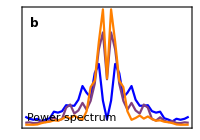

```mathematica
plotPspec=ListLinePlot[specData,
PlotRange->All,
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Automatic},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

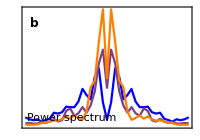

```mathematica
plotPspecNorm=ListLinePlot[specNormData,
PlotRange->All,
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Automatic},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.2cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.5cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+4*heightEws+heightBif+4*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotAc1,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxAc1,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotSmaxVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSmaxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotCv,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxCv,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th (top) row  *)
Inset[Show[plotTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspecNorm,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

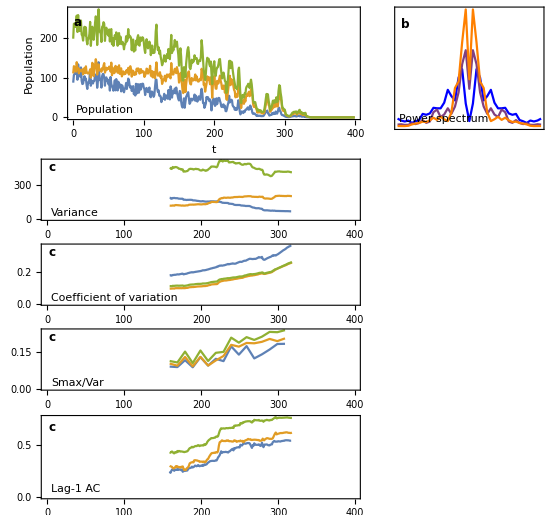

```mathematica
plotGrid
```

```mathematica
Export["figures/singles_"<>simName<>".png",plotGrid,ImageResolution->200];
```